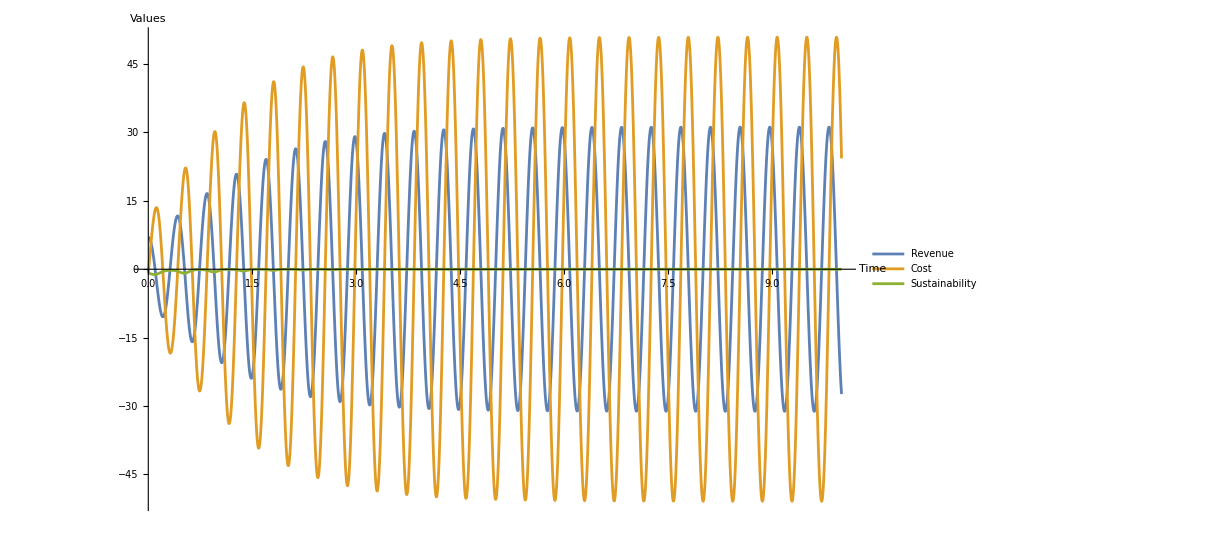

-Graphics3D-

```mathematica
Clear[r,c,s]

sol=NDSolve[
{
r'[t]==a (s[t] -c[t]),
c'[t]==b r[t]-k s[t] c[t],
s'[t]==s[t](r[t]-1),
r[0]==7,
c[0]==-√(2/3),
s[0]==-√(2/3),
a==4,
b==9,
k==24
},
{r,c,s},
{t,0,10000}
];

Plot[
Evaluate[{r[t],c[t],s[t]}/. sol],
{t,0,10},
AxesLabel->{"Time","Values"},
PlotLegends->Placed[{"Revenue","Cost","Sustainability"},{Right,Top}]]

ParametricPlot3D[
Evaluate[{r[t],c[t],s[t]}/. sol],
{t,0,10},
AxesLabel->{"r","c","s"},
BoxRatios->{1,1,1},
PlotLabel->"Phase Space Trajectory"]

(*Extract the solutions as interpolating functions*)
rFunc=r/. sol[[1]];
cFunc=c/. sol[[1]];
sFunc=s/. sol[[1]];

(*Sample data points*)
times=Range[0,1000,0.001]; (*Adjust the step size as needed*)
states=Table[{rFunc[t],cFunc[t],sFunc[t]},{t,times}];

(*Create the animation*)
DynamicModule[{index=1},
Dynamic@Graphics3D[
{
Red,Sphere[states[[index]],1] (*Adjust the sphere size*)
},
Boxed->True,
Axes->True,
AxesOrigin->{0,0,0},
AxesLabel->{"Revenue","Cost","Sustainability"},
PlotRange->{{-60,60},{-60,60},{-60,60}}
],
Initialization:>(
index=1;(*Reset index*)
RunScheduledTask[If[index<Length[states],index++,index=1],0.005] (*Update at intervals*)
)
]
```